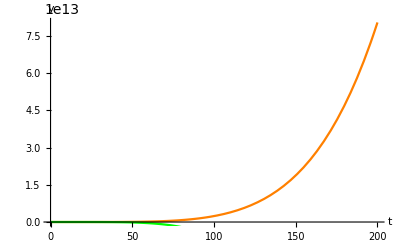

```mathematica
ivp:=NDSolve[{x1''[t]==-x2[t]*x1[t]^2-x2[t]^3,x2''[t]==x1[t]^3+x1[t]*x2[t]^2,x1[0]==1,x2[0]==5,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},{t,0,2}]

{x1soln[t_]} = {x1[t]} /. Flatten[NDSolve[{x1''[t]==-x2[t]*x1[t]^2-x2[t]^3,x2''[t]==x1[t]^3+x1[t]*x2[t]^2,x1[0]==0,x2[0]==0,x1'[0]==1,x2'[0]==1},{x1[t],x2[t]},{t,0,2}]];
{x2soln[t_]} = {x2[t]} /. Flatten[NDSolve[{x1''[t]==-x2[t]*x1[t]^2-x2[t]^3,x2''[t]==x1[t]^3+x1[t]*x2[t]^2,x1[0]==0,x2[0]==0,x1'[0]==1,x2'[0]==1},{x1[t],x2[t]},{t,0,2}]];
graphx1 = Plot[x1soln[t], {t, 0, 200}, AxesLabel -> {"t", "y"},PlotStyle->Orange];
graphx2 = Plot[x2soln[t], {t, 0, 200}, AxesLabel -> {"t", "y"},PlotStyle->Green];
Show[graphx1, graphx2]
```

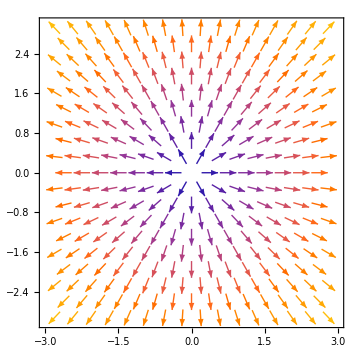

```mathematica
VectorPlot[{x1, x2}, {x1, -3, 3}, {x2, -3, 3}]
StreamPlot[{x1, x2}, {x1, -3, 3}, {x2, -3, 3}]
```

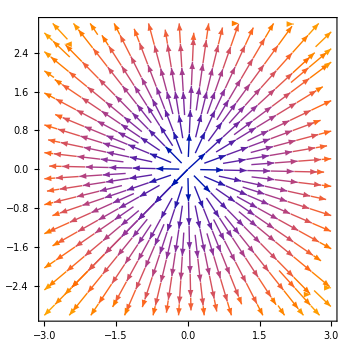

```mathematica
Exit[]
```

```mathematica
D[((x1^2+x2^2)*(-x2)), x1]/.x1->0/.x2->0
D[((x1^2+x2^2)*(-x2)), x2]/.x1->0/.x2->0
D[((x1^2+x2^2)*(x1)), x1]/.x1->0/.x2->0
D[((x1^2+x2^2)*(x1)), x2]/.x1->0/.x2->0
```

0

0

0

«1 more identical outputs»

```mathematica
D[(a*(x1^2+x2^2)*(x1)), x1]/.x1->0/.x2->0
D[(a*(x1^2+x2^2)*(x1)), x2]/.x1->0/.x2->0
D[(a*(x1^2+x2^2)*(x2)), x1]/.x1->0/.x2->0
D[(a*(x1^2+x2^2)*(x2)), x2]/.x1->0/.x2->0
```

0

0

0

«1 more identical outputs»